### Generate Comparison Figure

This file is used to perform correction of the emission rate produced according to the detector efficiency, and generate the figure of the comparison of theoretical and experimental result.

Copyright © 2018 Changkai Zhang
    Contact: phy.zhangck@gmail.com
    Licensed under GPL 3.0

First, read in the processed data from Processed.mx. We particularly need the emission rate Rate[θ].

```mathematica
<<(NotebookDirectory[]<>"/Processed.mx")
```

Define functions to generate the ratio of photon energies before and after the scattering, as well as the energy of scattered photons.

```mathematica
EngRatio[θ_]:=1/(1+(662/511)*(1-Cos[θ °]));
Energy[θ_]:=662*EngRatio[θ]
```

Compute the detection efficiency of the detector. According to the manual of the detector, the efficiency can be regarded as piecewise linearly dependent on the energy.

```mathematica
EfficiencyHigh[θ_]:=-1.2*10^-3*Energy[θ]+0.92;
EfficiencyLow[θ_]:=-2.7*10^-3*Energy[θ]+1.5;
EfficiencyHigh/@{15,30,35,45,55,60}~Join~(EfficiencyLow/@{70,85,95,105,115})
```

{0.159185,0.243088,0.27639,0.344115,0.408287,0.437888,0.125645,0.125673,0.12569,0.125706,0.125719}

Store the efficiency data in Efficiency[θ].

```mathematica
Do[Efficiency[angle]=EfficiencyHigh[angle],{angle,{15,30,35,45,55,60}}]
Do[Efficiency[angle]=EfficiencyLow[angle],{angle,{70,85,95,105,115}}]
```

Correct the emission rate according to the efficiency.

```mathematica
Do[RefinedRate[angle]=Rate[angle]/Efficiency[angle],{angle,{15,30,35,45,55,60,70,85,95,105,115}}]
```

```mathematica
RefinedRate/@{15,30,35,45,55,60,70,85,95,105,115}
```

{<|Value→2.61662,Error→0.0961852|>,<|Value→1.11155,Error→0.0434012|>,<|Value→0.64708,Error→0.0366188|>,<|Value→0.491631,Error→0.0171484|>,<|Value→0.377692,Error→0.0162718|>,<|Value→0.323508,Error→0.0158403|>,<|Value→0.25494,Error→0.0146234|>,<|Value→0.199429,Error→0.00464298|>,<|Value→0.180384,Error→0.00931518|>,<|Value→0.180294,Error→0.00526889|>,<|Value→0.174423,Error→0.00781552|>}

The theoretical results include the Thomson scattering from the classical Electrodynamics and Klein-Nishina formula from the quantum Electrodynamics. They are defined here.

```mathematica
KleinNishina[θ_]:=EngRatio[θ]^2*(EngRatio[θ]+EngRatio[θ]^-1-Sin[θ °]^2)/2;
Thomson[θ_]:=(1+Cos[θ °]^2)/2;
```

Due to the lack of luminosity information, the emission rate should be normalized. Normalization factor is adjusted manually.

```mathematica
NormFactor=1.15;Do[NormalizedRate[angle]=RefinedRate[angle]/NormFactor,{angle,{15,30,35,45,55,60,70,85,95,105,115}}]
```

Combine the angle info to generate data for plot.

```mathematica
PlotData=MapThread[Prepend,{Values[NormalizedRate/@{15,30,35,45,55,60,70,85,95,105,115}],{15,30,35,45,55,60,70,85,95,105,115}}];
```

Preview the plot.

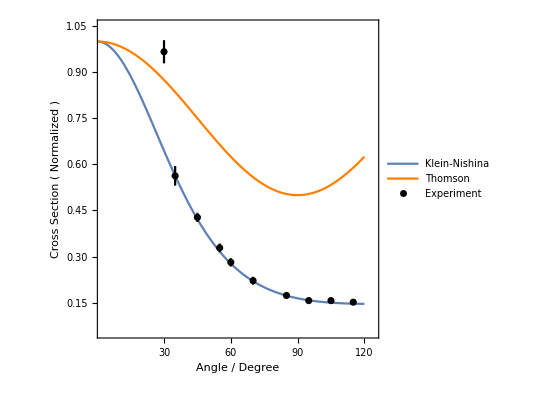

```mathematica
Needs["ErrorBarPlots`"]
Show[Plot[KleinNishina[θ],{θ,0,120},PlotLegends->Placed[{"Klein-Nishina"},{Top,Right}]],Plot[Thomson[θ],{θ,0,120},PlotStyle->Orange,PlotLegends->Placed[{"Thomson"},{Top,Right}]],ErrorListPlot[PlotData,PlotStyle->Black,PlotLegends->Placed[{"Experiment"},{Top,Right}]],PlotRange-> {{2.5,124},{0.055,1.05}},AxesOrigin->{0,0},AspectRatio->1,Frame->{True,True,False,False},FrameLabel->{"Angle / Degree","Cross  Section  ( Normalized  )"},LabelStyle->{FontSize->12}]
```

A magnified plot is generated and refined here.

```mathematica
Result=Show[Plot[KleinNishina[θ],{θ,0,120},PlotStyle->{AbsoluteThickness[4]},PlotLegends->Placed[{"Klein-Nishina    "},{{.6,.83},{0.02,0.5}}],LabelStyle->{FontSize->42}],Plot[Thomson[θ],{θ,0,120},PlotStyle->{Orange,AbsoluteThickness[4]},PlotLegends->Placed[{"Thomson    "},{{.6,.9},{0.03,0.5}}],LabelStyle->{FontSize->42}],ErrorListPlot[PlotData,PlotStyle->{Black,AbsoluteThickness[4]},PlotLegends->Placed[{"Experiment"},{{.6,.76},{0,0.5}}],LabelStyle->{FontSize->42}],PlotRange-> {{2.5,124},{0.055,1.05}},AxesOrigin->{0,0},AspectRatio->1,Frame->{True,True,False,False},FrameStyle->Directive[Thickness[0.003],Gray],FrameTicksStyle->Directive[Thickness[.003],Gray],FrameLabel->{"\nAngle / Degree","Cross  Section  ( Normalized  )\n"},LabelStyle->{FontSize->42},ImageSize->1000];
```

Export the graph to Result.png in the same directory.

```mathematica
Export[NotebookDirectory[]<>"/Result.png",Result]
```

C:\Users\lenovo\Desktop\Compton\/Result.png

This is the end of file Generate.nb. Current version: release-0.0.1.0. Started March 31, 2018. Finished April 1, 2018. Last Revised April 4, 2018.